## Calculation of the Greens function and the dynamic adjoint in two-group theory with a unified code for both thermal and fast reactors

```mathematica
SetDirectory[NotebookDirectory[]]; SetOptions[$FrontEnd,Magnification->1.5];
```

```mathematica
Input data: The  Behringer-Kosály-Pázsit 1979 NSE article (BWR) and Zsolti's various .json files for github.
```

### BKP 1979 data (BWR)

```mathematica
Subscript[D, 1]=1.709;     (* BKP *)
Subscript[D, 2]= 0.5290;
Subscript[νΣ, f1]= 0.004653;   (*   x 1.11 for the small system *)
Subscript[νΣ, f2]= 0.07254;      (*   x 1.11 for the small system *)
Subscript[Σ, a1]=0.00733;
Subscript[Σ, a2]= 0.05940;
Subscript[Σ, R]=0.01271;
Subscript[Σ, 2]=Subscript[Σ, a2];
β=0.007;
λ=0.1;
Subscript[v, 1]=1.7549*^7;
Subscript[v, 2]=3.9040*^5;
Subscript[χ, p1]=1;
Subscript[χ, d1]=1;
Subscript[χ, p2]=0;
Subscript[χ, d2]=0;
Subscript[χ, 1]=(1-β)*Subscript[χ, p1]+β*Subscript[χ, d1];
Subscript[χ, 2]=(1-β)*Subscript[χ, p2]+β*Subscript[χ, d2];
Print["D_1= ",Subscript[D, 1],"   D_2= ",Subscript[D, 2], "   νΣ_f1= ",Subscript[νΣ, f1],"  νΣ_f2= ",Subscript[νΣ, f2]];
Print["Σ_a1= ",Subscript[Σ, a1],"  Σ_1= ",Subscript[Σ, 1], "   Σ_R= ",Subscript[Σ, R],"  Σ_a2= ",Subscript[Σ, a2] ];
Print["   β= ",β,"  λ= ",λ" v_1= ",Subscript[v, 1]"   v_2= ",Subscript[v, 2]];
Print["χ_p1 = ",Subscript[χ, p1],"    χ_d1 = ",Subscript[χ, d1],"    χ_p2 = ",Subscript[χ, p2],"    χ_d2 = ",Subscript[χ, d2]];
Print["χ_1 = ",Subscript[χ, 1],"    χ_2 = ",Subscript[χ, 2]];
```

D_1= 1.709   D_2= 0.529   νΣ_f1= 0.004653  νΣ_f2= 0.07254

Σ_a1= 0.00733  Σ_1= 0.0148752   Σ_R= 0.01271  Σ_a2= 0.0594

β= 0.007  λ= 0.1  v_1= 1.7549×10^7    v_2= 390400.

χ_p1 = 1    χ_d1 = 1    χ_p2 = 0    χ_d2 = 0

χ_1 = 1.    χ_2 = 0.

### Importing data from Zsolti’s file

Choose the input .json file from the directory: choose from
sfrcoresimple_inf   (Zsolti’s SFR)
msfr_inf                      (Katy Huff/Samofar)
msfr_ergi_inf          (Samofar, with χ_p1 etc. values, i=1,2,...)  This is a large core, rather space-dependent
lfrsmr_b1.json        (this is something Zsolti generated, do not know where from. Medium large reactor, not large)

```mathematica
data = Import["https://raw.githubusercontent.com/imre-chalmers-se/IET_book/refs/heads/main/data/msfr_erg4_inf.json","JSON"];
```

```mathematica
Subscript[D, 1]=("D1" /. data);
Subscript[D, 2] =("D2" /. data);
Subscript[νΣ, f1]=("nuSig1" /. data);
Subscript[νΣ, f2]=("nuSig2" /. data);
Subscript[Σ, a1]=("Siga1" /. data);
Subscript[Σ, 1]=("SigR1" /. data);
Subscript[Σ, R]=Subscript[Σ, 1]-Subscript[Σ, a1];
Subscript[Σ, a2]=("Siga2" /. data);
β=("beta0" /. data);
λ=("lambda" /. data);
Subscript[v, 1]=("v1" /. data);
Subscript[v, 2]=("v2" /. data);
Print["D_1= ",Subscript[D, 1],"   D_2= ",Subscript[D, 2], "   νΣ_f1= ",Subscript[νΣ, f1],"  νΣ_f2= ",Subscript[νΣ, f2]];
Print["Σ_a1= ",Subscript[Σ, a1],"  Σ_1= ",Subscript[Σ, 1], "   Σ_R= ",Subscript[Σ, R],"  Σ_a2= ",Subscript[Σ, a2] ];
Print["   β= ",β,"  λ= ",λ",v_1= ",Subscript[v, 1],"   v_2= ",Subscript[v, 2]];
```

D_1= 1.75736   D_2= 1.04221   νΣ_f1= 0.00405111  νΣ_f2= 0.00724195

Σ_a1= 0.00260927  Σ_1= 0.032988   Σ_R= 0.0303787  Σ_a2= 0.00752808

β= 0.00308517  λ= 0.325805 ,v_1= 1.46022×10^9   v_2= 1.04137×10^8

Some further data: spectral indices and delayed neutron data

```mathematica
Subscript[χ, p1]=("Chi1p" /. data);
Subscript[χ, d1]=("Chi1d" /. data);
Subscript[χ, p2]=("Chi2p" /. data);
Subscript[χ, d2]=("Chi2d" /. data);
β=("beta0" /. data);
Subscript[χ, 1]=(1-β)*Subscript[χ, p1]+β*Subscript[χ, d1];
Subscript[χ, 2]=(1-β)*Subscript[χ, p2]+β*Subscript[χ, d2];
λ=("lambda" /. data);
Print["χ_p1 = ",Subscript[χ, p1],"    χ_d1 = ",Subscript[χ, d1],"    χ_p2 = ",Subscript[χ, p2],"    χ_d2 = ",Subscript[χ, d2]];
Print["χ_1 = ",Subscript[χ, 1],"    χ_2 = ",Subscript[χ, 2],"    β = ",β,"    λ = ",λ];
```

χ_p1 = 0.879597    χ_d1 = 0.371764    χ_p2 = 0.120403    χ_d2 = 0.628236

χ_1 = 0.87803    χ_2 = 0.12197    β = 0.00308517    λ = 0.325805

### Start the calculation

Calculation of the roots of the characteristic equation and the critical size - fast system

Define the new variables and do the calculations

```mathematica
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R]-Subscript[χ, 1] Subscript[νΣ, f1];
Subscript[Σ, 2]=Subscript[Σ, a2]-Subscript[χ, 2] Subscript[νΣ, f2];
Subscript[Σ, R2]=Subscript[Σ, R]+Subscript[χ, 2] Subscript[νΣ, f1];
Subscript[k, ∞]=(Subscript[χ, 1] Subscript[νΣ, f1] Subscript[Σ, a2]+Subscript[χ, 2] Subscript[νΣ, f2] Subscript[Σ, a1]+Subscript[νΣ, f2] Subscript[Σ, R])/(Subscript[Σ, a2] (Subscript[Σ, a1]+Subscript[Σ, R]));Subscript[L2, 1]=Subscript[D, 1]/Subscript[Σ, 1];   Subscript[L2, 2]=Subscript[D, 2]/Subscript[Σ, 2];  
B2=-1/2(1/Subscript[L2, 1]+1/Subscript[L2, 2])+1/2 √((1/Subscript[L2, 1]+1/Subscript[L2, 2])^2+4(Subscript[χ, 1] Subscript[νΣ, f2] Subscript[Σ, R2] - Subscript[Σ, 1] Subscript[Σ, 2])/(Subscript[D, 1] Subscript[D, 2]));
Nu2=1/2(1/Subscript[L2, 1]+1/Subscript[L2, 2])+1/2 √((1/Subscript[L2, 1]+1/Subscript[L2, 2])^2+4(Subscript[χ, 1] Subscript[νΣ, f2] Subscript[Σ, R2] - Subscript[Σ, 1] Subscript[Σ, 2])/(Subscript[D, 1] Subscript[D, 2]));
B = √B2; H = π/B; a=H/2; Nu = √Nu2;
spectralindex =(Subscript[χ, 1] Subscript[νΣ, f2])/(Subscript[Σ, 1]+ Subscript[D, 1] B2);
Print["B^2 = ",B2,"B = ",B,"    Nu = ",Nu];
Print["k_∞=", Subscript[k, ∞], "        L_1^2 = ",Subscript[L2, 1]," [cm]"," L_2^2 = ",Subscript[L2, 2]," [cm]"];
Print["H = ",H, " [cm]","   a = ",a, " [cm]"];
Print["ϕ_1/ϕ_2 = ",spectralindex]
```

B^2 = 0.0000176266B = 0.0041984    Nu = 0.15212

k_∞=1.00301        L_1^2 = 59.7112 [cm] L_2^2 = 156.846 [cm]

H = 748.283 [cm]   a = 374.141 [cm]

ϕ_1/ϕ_2 = 0.215826

### Collapsing the geometry from 3D to 1D

```mathematica
a=220;B2diff = B2 - (π/(2a))^2;
```

Modify the absorption and the total cross sections by accounting leakage

```mathematica
Subscript[Σ, a1]=Subscript[Σ, a1]+Subscript[D, 1]*B2diff; Subscript[Σ, a2]=Subscript[Σ, a2]+Subscript[D, 2]*B2diff;
Subscript[Σ, 1]=Subscript[Σ, a1]+Subscript[Σ, R]-Subscript[χ, 1] Subscript[νΣ, f1];
Subscript[Σ, 2]=Subscript[Σ, a2]-Subscript[χ, 2] Subscript[νΣ, f2];
```

Re-calculate the static buckling with these values

```mathematica
Subscript[k, ∞]=(Subscript[χ, 1] Subscript[νΣ, f1] Subscript[Σ, a2]+Subscript[χ, 2] Subscript[νΣ, f2] Subscript[Σ, a1]+Subscript[νΣ, f2] Subscript[Σ, R])/(Subscript[Σ, a2] (Subscript[Σ, a1]+Subscript[Σ, R])); Subscript[L2, 1]=Subscript[D, 1]/Subscript[Σ, 1];   Subscript[L2, 2]=Subscript[D, 2]/Subscript[Σ, 2];  
B2=-1/2(1/Subscript[L2, 1]+1/Subscript[L2, 2])+1/2 √((1/Subscript[L2, 1]+1/Subscript[L2, 2])^2+4(Subscript[χ, 1] Subscript[νΣ, f2] Subscript[Σ, R2] - Subscript[Σ, 1] Subscript[Σ, 2])/(Subscript[D, 1] Subscript[D, 2]));
Nu2=1/2(1/Subscript[L2, 1]+1/Subscript[L2, 2])+1/2 √((1/Subscript[L2, 1]+1/Subscript[L2, 2])^2+4(Subscript[χ, 1] Subscript[νΣ, f2] Subscript[Σ, R2] - Subscript[Σ, 1] Subscript[Σ, 2])/(Subscript[D, 1] Subscript[D, 2]));
(* B2sfr=(π/100)^2+(2.405/244)^2; *)
B = √B2; H = π/B; a=H/2; Nu = √Nu2;
Print["B^2 = ",B2,"    B = ",B,"    Nu = ",Nu];
Print["k_∞=", Subscript[k, ∞], "        L_1^2 = ",Subscript[L2, 1]," [cm]"," L_2^2 = ",Subscript[L2, 2]," [cm]"];
Print["H = ",H, " [cm]","   a = ",a, " [cm]"]
```

B^2 = 0.0000509794    B = 0.00713998    Nu = 0.152011

k_∞=1.00874        L_1^2 = 59.8303 [cm] L_2^2 = 157.671 [cm]

H = 440. [cm]   a = 220. [cm]

### Calculating the dynamic variables - fast system

```mathematica
chi1[ω_]= Subscript[χ, p1](1-β)+(β λ)/(ⅈ ω+λ)Subscript[χ, d1];
chi2[ω_]= Subscript[χ, p2](1-β)+(β λ)/(ⅈ ω+λ)Subscript[χ, d2];
Sig1[ω_]:=Subscript[Σ, a1]+(ⅈ ω)/Subscript[v, 1]+Subscript[Σ, R]-chi1[ω]*Subscript[νΣ, f1]; 
Sig2[ω_]:=Subscript[Σ, a2]+(ⅈ ω)/Subscript[v, 2]-chi2[ω]*Subscript[νΣ, f2];
SigR2[ω_]:=Subscript[Σ, R]+chi2[ω]* Subscript[νΣ, f1];
Nusf2[ω_]:=chi1[ω]*Subscript[νΣ, f2];
```

```mathematica
μ[ω_]:=√(-1/2(Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])+1/2 √((Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])^2+4(SigR2[ω]*Nusf2[ω]-Sig1[ω]*Sig2[ω])/(Subscript[D, 1] Subscript[D, 2])));
ν[ω_]:=√(1/2(Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])+1/2 √((Sig1[ω]/Subscript[D, 1]+Sig2[ω]/Subscript[D, 2])^2+4(SigR2[ω]*Nusf2[ω]-Sig1[ω]*Sig2[ω])/(Subscript[D, 1] Subscript[D, 2])));
Subscript[c, μ][ω_]:=(Sig1[ω]+Subscript[D, 1] μ[ω]^2)/Nusf2[ω];  Subscript[c, ν][ω_]:=(Sig1[ω]-Subscript[D, 1] ν[ω]^2)/Nusf2[ω]
```

Calculation of the Greens matrix

Define the basic solutions g_μ and g_⋁ as piecewise functions.

```mathematica
Subscript[g, μ][x_,x0_,ω_]:= Piecewise[{{Sin[μ[ω](a+x)]Sin[μ[ω](a-x0)],x<x0},
{Sin[μ[ω](a-x)]Sin[μ[ω](a+x0)],x0<=x}}];
Subscript[g, ν][x_,x0_,ω_]:= Piecewise[{{Sinh[ν[ω](a+x)]Sinh[ν[ω](a-x0)],x<x0},
{Sinh[ν[ω](a-x)]Sinh[ν[ω](a+x0)],x0<=x}}];
```

Define c_μ and c_ν

```mathematica
Subscript[c, μ][ω_]:=(Sig1[ω]+Subscript[D, 1] μ[ω]^2)/Nusf2[ω];  Subscript[c, ν][ω_]:=(Sig1[ω]-Subscript[D, 1] ν[ω]^2)/Nusf2[ω]
```

Define the coefficiens A_μ1..... A_ν2 .

```mathematica
Subscript[A, μ1][ω_]:=(Subscript[c, ν][ω] Nusf2[ω])/((Subscript[D, 1])^2 μ[ω]Sin[2 μ[ω] a](μ[ω]^2+ν[ω]^2));
Subscript[A, ν1][ω_]:=-(Subscript[c, μ][ω]Nusf2[ω])/((Subscript[D, 1])^2 ν[ω]Sinh[2 ν[ω] a](μ[ω]^2+ν[ω]^2));
Subscript[A, μ2][ω_]:=-Nusf2[ω]/(Subscript[D, 1] Subscript[D, 2] μ[ω]Sin[2 μ[ω] a](μ[ω]^2+ν[ω]^2));
Subscript[A, ν2][ω_]:=Nusf2[ω]/(Subscript[D, 1] Subscript[D, 2] ν[ω]Sinh[2 ν[ω] a](μ[ω]^2+ν[ω]^2));
```

Define the Green matrix elements G_11, G_12, G_21 and G_22

```mathematica
Subscript[G, 11][x_,x0_,ω_]:=Subscript[A, μ1][ω]Subscript[g, μ][x,x0,ω]+Subscript[A, ν1][ω]Subscript[g, ν][x,x0,ω];
Subscript[G, 21][x_,x0_,ω_]:=Subscript[c, μ][ω]Subscript[A, μ1][ω]Subscript[g, μ][x,x0,ω]+Subscript[c, ν][ω]Subscript[A, ν1][ω]Subscript[g, ν][x,x0,ω];
Subscript[G, 12][x_,x0_,ω_]:=Subscript[A, μ2][ω]Subscript[g, μ][x,x0,ω]+Subscript[A, ν2][ω]Subscript[g, ν][x,x0,ω];
Subscript[G, 22][x_,x0_,ω_]:=Subscript[c, μ][ω]Subscript[A, μ2][ω]Subscript[g, μ][x,x0,ω]+Subscript[c, ν][ω]Subscript[A, ν2][ω]Subscript[g, ν][x,x0,ω];
```

Plot the space dependence of the absolute value of the four elements of the Green’s matrix with the BWR data of the B-K-P article, as functions of the x variable, for a central perturbation (x_0=0) and ω = 10 rad/s

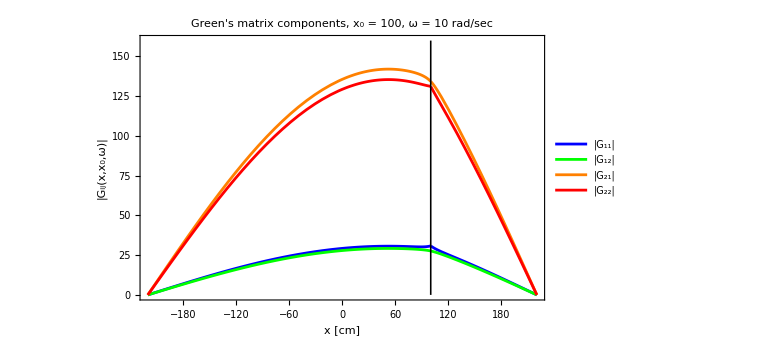

```mathematica
ClearAll[x];x0 = 100; ω =10;
values =Flatten[Table[{Abs[Subscript[G, 11][x,x0,ω]],Abs[Subscript[G, 12][x,x0,ω]],Abs[Subscript[G, 21][x,x0,ω]],Abs[Subscript[G, 22][x,x0,ω]]},{x,x0-50,x0+50,a/100}]];
{roundedMin,roundedMax}=[values,20];
Show[Plot[{Abs[Subscript[G, 11][x,x0,ω]],Abs[Subscript[G, 12][x,x0,ω]],Abs[Subscript[G, 21][x,x0,ω]],Abs[Subscript[G, 22][x,x0,ω]]},{x,-a,a},PlotRange -> {0,roundedMax},Frame->True,FrameLabel->{"x [cm]","|G_ij(x,x_0,ω)|"},PlotLegends->Placed[LineLegend[{"|G_11|","|G_12|","|G_21|","|G_22|"},LabelStyle->{FontSize->14}],{0.9,0.76}], PlotLabel->"Green's matrix components, x_0 = "<> ToString[x0] <>", ω = "<> ToString[ω ]<>" rad/sec" ,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->Large, PlotStyle->{Blue,Green, Orange, Red}],Epilog->{Thickness[0.002],Line[{{x0,0},{x0,roundedMax}}]}]
```

```mathematica
ArgDeg[z_]:=Arg[z]*180/π;
```

Plot the space dependence of the phase of the four elements of the Green’s matrix in degrees, as functions of the x variable, for a perturbation at x_0 and ω = 10 rad/s

```mathematica
ClearAll[x];x0 = 00; ω =10;
Show[Plot[{ArgDeg[-Subscript[G, 11][x,x0,ω]],ArgDeg[-Subscript[G, 12][x,x0,ω]],ArgDeg[-Subscript[G, 21][x,x0,ω]],ArgDeg[-Subscript[G, 22][x,x0,ω]]},{x,-a,a},PlotRange -> {-10,0},Frame->True,FrameLabel->{"x [cm]","Phase [degrees]"},PlotLegends->Placed[LineLegend[{"φ(G_11)","φ(G_12)","φ(G_21)","φ(G_22)"},LabelStyle->{FontSize->14}],{0.85,0.65}], PlotLabel->"Phase of G_ij(x,x_0,ω), x_0 = "<> ToString[x0] <>", ω = "<> ToString[ω ]<>" rad/sec" ,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->Large, PlotStyle->{Blue,Green, Orange, Red}],Epilog->{Thickness[0.0015],Line[{{x0,-15},{x0,0}}]}]
```

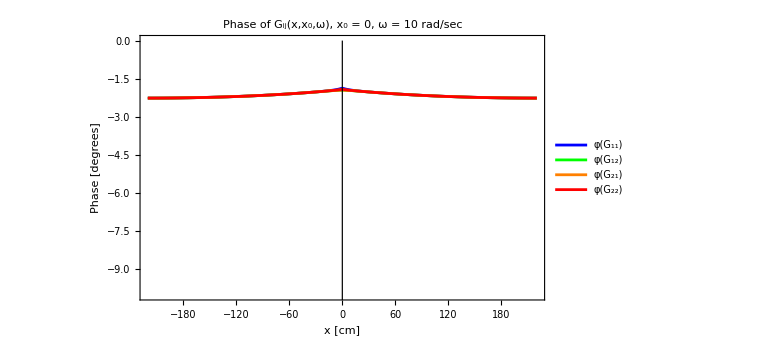

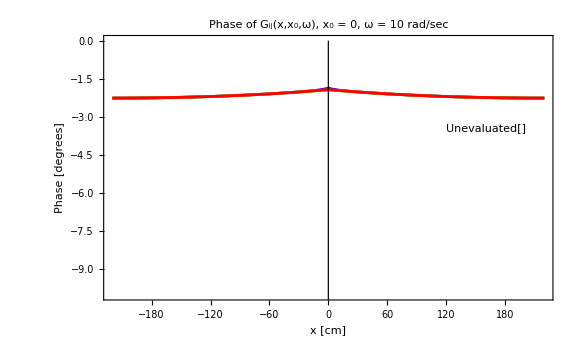

Plot the space dependence of the amplitude of the “fast removal Green’s function” G_11-G_12, which yields the noise in the fast group, induced by the fluctuations of the removal cross section Σ_R: (no equivalence with the dynamic adjoint of Hugo):

```mathematica
ClearAll[x];x0=0;ω=10;
values =MaxValue[Abs[Subscript[G, 11][x,x0,ω]-Subscript[G, 12][x,x0,ω]],x];
{roundedMin,roundedMax}=[values,1];Plot[Abs[Subscript[G, 11][x,x0,ω]-Subscript[G, 12][x,x0,ω]],{x,-a,a},PlotRange -> {0,roundedMax},Frame->True,FrameLabel->{"x [cm]","|G_11(x,x_0,ω)-G_12(x,x_0,ω)|"},PlotLegends->"Expressions",BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotLabel->"Fast removal Green's fct, x_0 = " <> ToString[x0] <> ", ω = " <> ToString[ω] <> " rad/sec", ImageSize->Large]
```

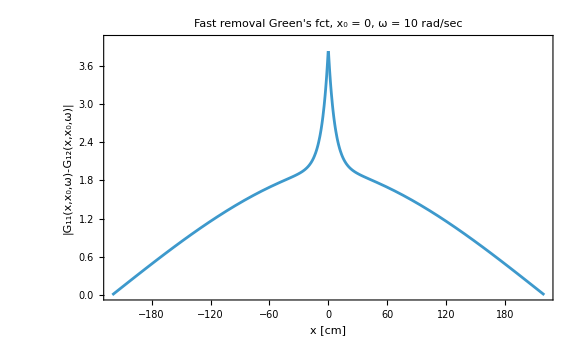

Plot the space dependence of the phase of the “fast removal Green’s function” G_11-G_12, which yields the noise in the fast group, induced by the fluctuations of the removal cross section Σ_R: (no equivalence with the dynamic adjoint of Hugo):

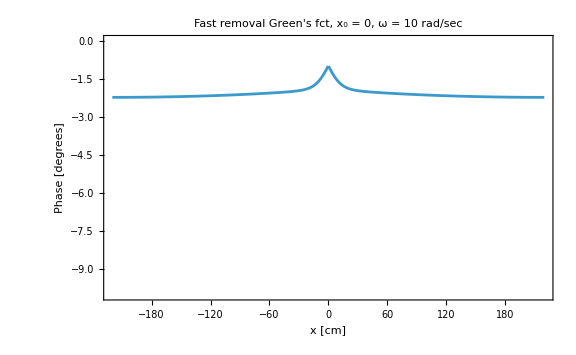

```mathematica
ClearAll[x];x0=0;ω=10;Plot[ArgDeg[-Subscript[G, 11][x,x0,ω]+Subscript[G, 12][x,x0,ω]],{x,-a,a},PlotRange -> {-10,0},Frame->True,FrameLabel->{"x [cm]","Phase [degrees]"},PlotLegends->"Expressions",BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotLabel->"Fast removal Green's fct, x_0 = " <> ToString[x0] <> ", ω = " <> ToString[ω] <> " rad/sec", ImageSize->Large]
```

Plot the space dependence of the absolute value of the “thermal removal Green’s function” G_21-G_22, which yields the noise in the thermal group, induced by the fluctuations of the removal cross section Σ_R: (the same as ψ_1^† - ψ_2^† in the B-K-P article):

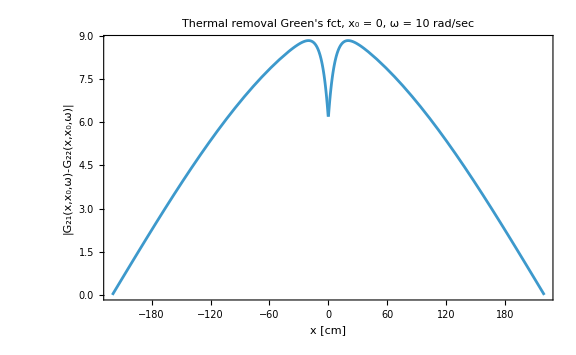

```mathematica
ClearAll[x];x0=0;ω=10;Plot[Abs[Subscript[G, 21][x,x0,ω]-Subscript[G, 22][x,x0,ω]],{x,-a,a},PlotRange -> Automatic,Frame->True,FrameLabel->{"x [cm]","|G_21(x,x_0,ω)-G_22(x,x_0,ω)|"},(*PlotLegends->Placed["Expressions",{0.8,0.8}],*)BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotLabel->"Thermal removal Green's fct, x_0 = " <> ToString[x0] <> ", ω = " <> ToString[ω] <> " rad/sec", ImageSize->Large]
```

Plot the space dependence of the phase of the “fast removal Green’s function” G_11-G_12, which yields the noise in the fast group, induced by the fluctuations of the removal cross section Σ_R: (no equivalence with the dynamic adjoint of Hugo):

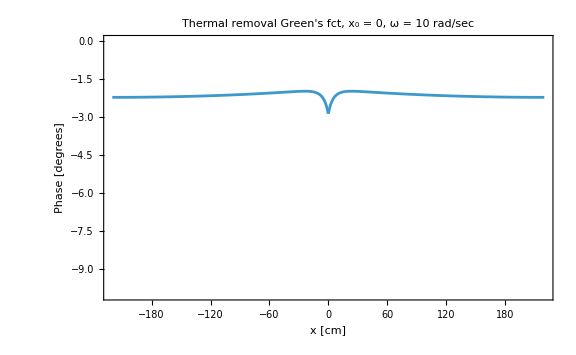

```mathematica
ClearAll[x];x0=0;ω=10;Plot[ArgDeg[-Subscript[G, 21][x,x0,ω]+Subscript[G, 22][x,x0,ω]],{x,-a,a},PlotRange -> {-10,0},Frame->True,FrameLabel->{"x [cm]","Phase [degrees]"},(*PlotLegends->"Expressions",*)BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotLabel->"Thermal removal Green's fct, x_0 = " <> ToString[x0] <> ", ω = " <> ToString[ω] <> " rad/sec", ImageSize->Large]
```

Plot the frequency dependence of the amplitude of the four elements of the Green’s matrix with the BWR data of the B-K-P article

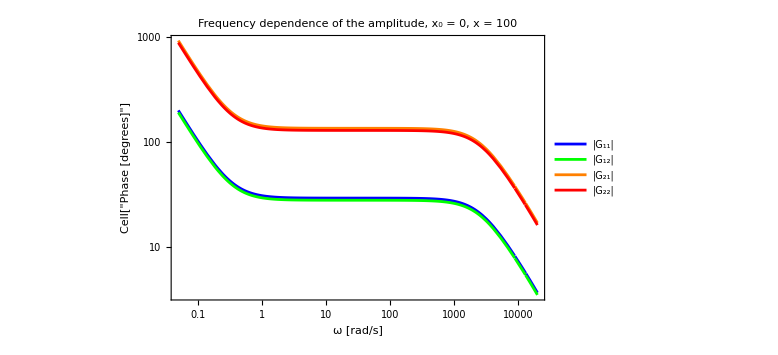

```mathematica
ClearAll[ω];x0=0; x =100;
LogLogPlot[{Abs[Subscript[G, 11][x,x0,ω]],Abs[Subscript[G, 12][x,x0,ω]],Abs[Subscript[G, 21][x,x0,ω]],Abs[Subscript[G, 22][x,x0,ω]]},{ω,5*^-2,2*^4},PlotRange -> Automatic,Frame->True,Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,0,4}]},FrameLabel->{"ω [rad/s]","Cell["Phase [degrees]",ExpressionUUID->"909aeaef-b6a8-48f1-8230-aef55b7c5216"]"},PlotLegends->Placed[LineLegend[{"|G_11|","|G_12|","|G_21|","|G_22|"},LabelStyle->{FontSize->14}],{0.85,0.8}],BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotLabel->"Frequency dependence of the amplitude, x_0 = " <> ToString[x0] <> ", x = " <> ToString[x] , PlotStyle->{Blue,Green, Orange, Red},ImageSize->Large]
```

Plot the frequency dependence of the phase of the four elements of the Green’s matrix with the BWR data of the B-K-P article

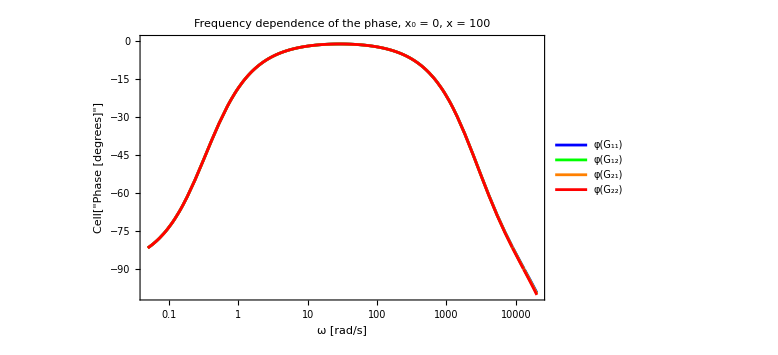

```mathematica
x0 =0;x=100;
LogLinearPlot[{ArgDeg[-Subscript[G, 11][x,x0,ω]],ArgDeg[-Subscript[G, 12][x,x0,ω]],ArgDeg[-Subscript[G, 21][x,x0,ω]],ArgDeg[-Subscript[G, 22][x,x0,ω]]},{ω,5*^-2,2*^4},PlotRange -> Automatic,Frame->True,(*Ticks->{Automatic,Table[{10^i,Superscript[10,i]},{i,0,4}]},*)FrameLabel->{"ω [rad/s]","Cell["Phase [degrees]",ExpressionUUID->"efb913cd-ad9a-423d-b6ca-8405b9795b0b"]"},PlotLegends->Placed[LineLegend[{"φ(G_11)","φ(G_12)","φ(G_21)","φ(G_22)"},LabelStyle->{FontSize->14}],{0.55,0.6}],BaseStyle->{FontFamily->"Helvetica",FontSize->18},PlotLabel->"Frequency dependence of the phase, x_0 = " <> ToString[x0] <> ", x = " <> ToString[x] , PlotStyle->{Blue,Green, Orange, Red},ImageSize->Large]
```